```mathematica
mytable = {};
For[r=0,r<6,r+=0.01,
	x = {0.5};
	For[i=2, i≤80, i++,
		 If[x[[i-1]]>0.001, 
			AppendTo[x,r*x[[i-1]]*(1-x[[i-1]])],
			AppendTo[x,0]]
             ]
    AppendTo[mytable, x]
]
```

```mathematica
Length[mytable]
```

600

```mathematica
Manipulate[ListLinePlot[mytable[[r]]],{r,0,600}]
```

ListLinePlot::lpn: List is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression 448. cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: {{0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«30»},«49»,«550»}⟦448.⟧ is not a list of numbers or pairs of numbers.

```mathematica
mytable[[1]][[2]]
```

0.

```mathematica
Table[{r,mytable[[r]][[60]]},{r,0,4}]
```

Part::partd: Part specification List⟦60⟧ is longer than depth of object.

{{0,List⟦60⟧},{1,0},{2,0},{3,0},{4,0}}

```mathematica
mylist={};
For[r=1,r<600,r+=1,
AppendTo[mylist,mytable[[r]][[80]] ]
]
mylist2={};
For[r=1,r<600,r+=1,
AppendTo[mylist2,mytable[[r]][[79]] ]
]
mylist3={};
For[r=1,r<600,r+=1,
AppendTo[mylist3,mytable[[r]][[78]] ]
]
mylist4={};
For[r=1,r<600,r+=1,
AppendTo[mylist4,mytable[[r]][[77]] ]
]
mylist5={};
For[r=1,r<600,r+=1,
AppendTo[mylist5,mytable[[r]][[76]] ]
]
mylist6={};
For[r=1,r<600,r+=1,
AppendTo[mylist6,mytable[[r]][[75]] ]
]
mylist7={};
For[r=1,r<600,r+=1,
AppendTo[mylist7,mytable[[r]][[74]] ]
]
mylist8={};
For[r=1,r<600,r+=1,
AppendTo[mylist8,mytable[[r]][[73]] ]
]
```

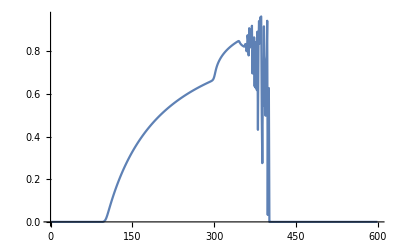

```mathematica
ListLinePlot[mylist]
```

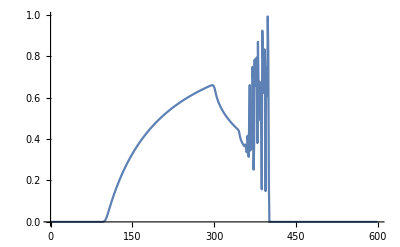

```mathematica
ListLinePlot[mylist2]
```

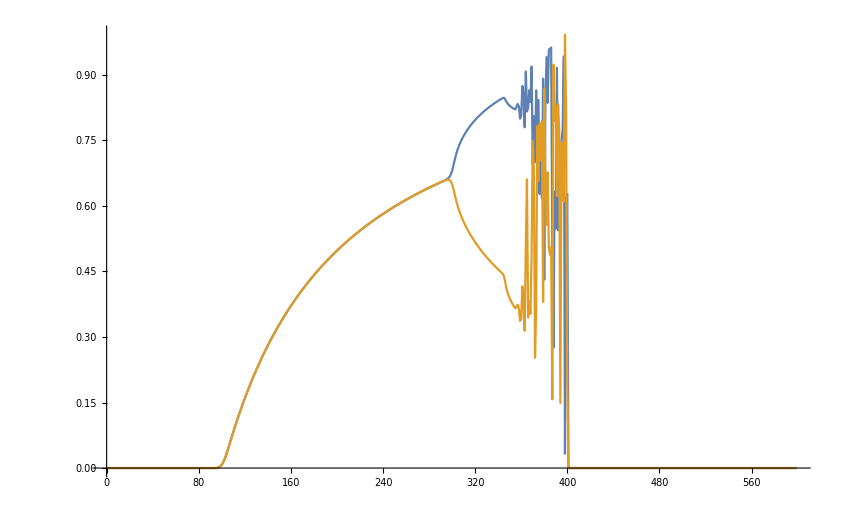

```mathematica
ListLinePlot[{mylist,mylist2}]
```

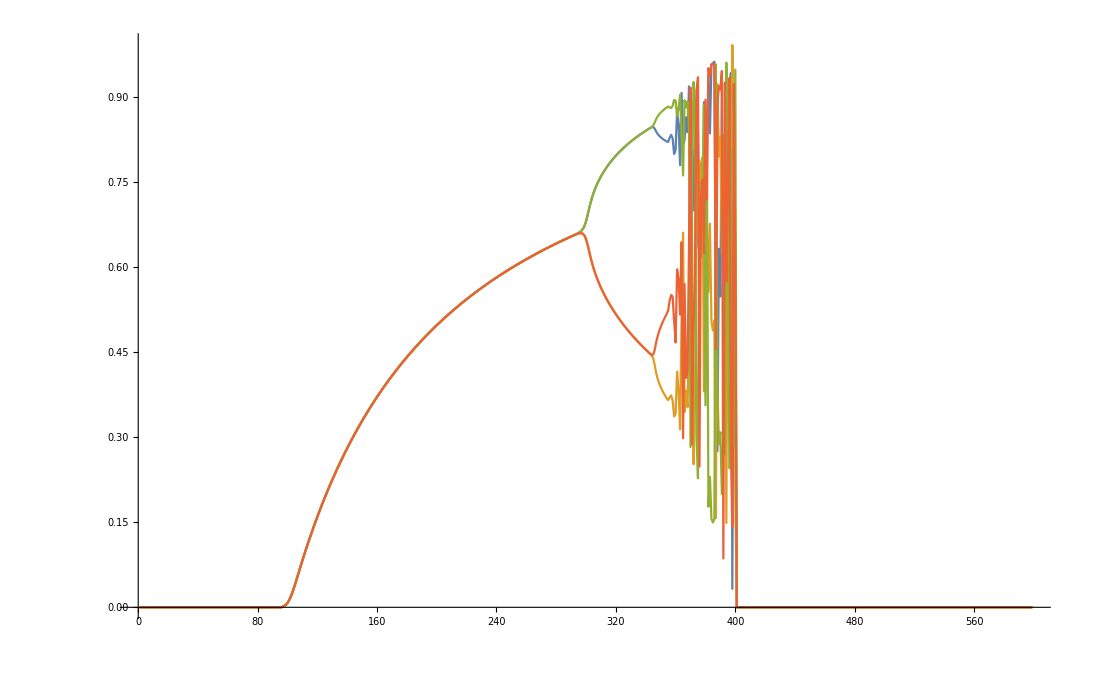

```mathematica
ListLinePlot[{mylist,mylist2,mylist3,mylist4}]
```

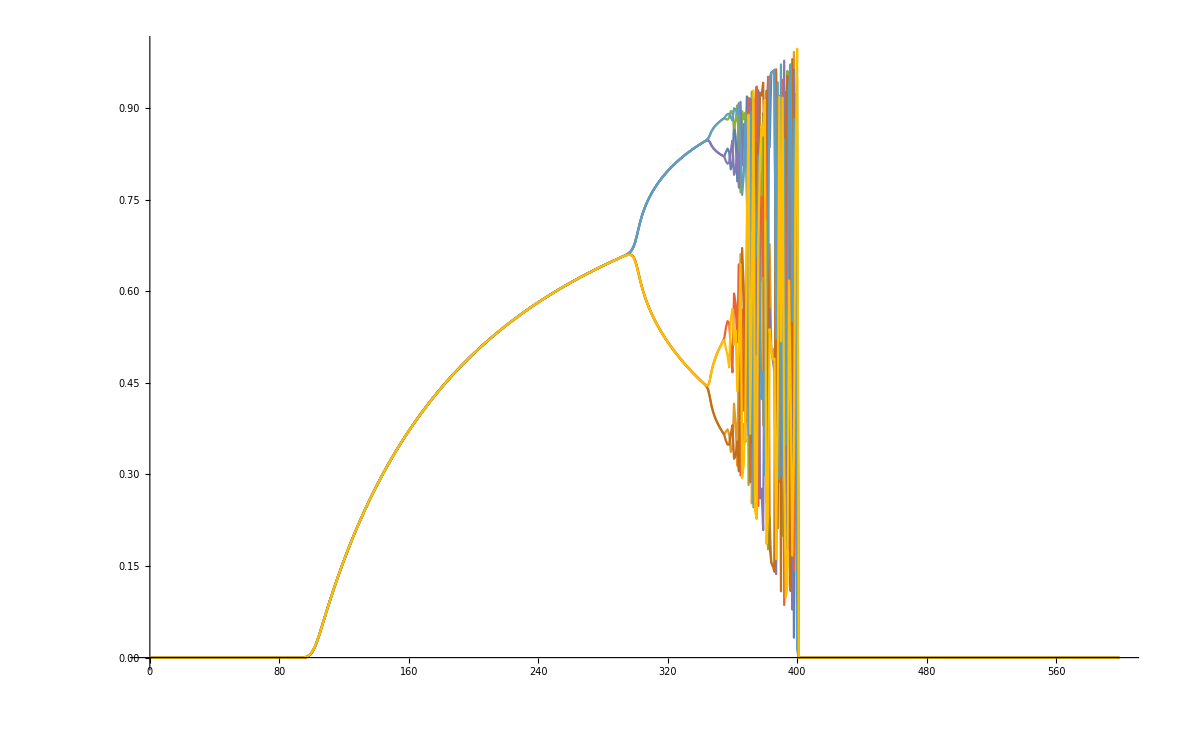

```mathematica
ListLinePlot[{mylist,mylist2,mylist3,mylist4,mylist5,mylist6,mylist7,mylist8}]
```